```mathematica
f[z_]=(z-1)^2(z+1); Lf[z_]=f[z]f''[z]/f'[z]^2; sc[z_]=z-f[z]/f'[z]/(1-Lf[z])//Simplify
```

(1+6 z+z^2)/(3+2 z+3 z^2)

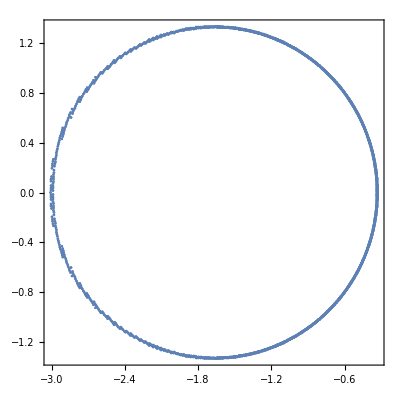

```mathematica
JuliaSetPlot[(1+6 z+z^2)/(3+2 z+3 z^2),z,ColorFunction->None]
```

```mathematica
moeb[z_]=(z-1)/(z+1); invmoeb[z_]=(-1*z-1)/(z-1); sc2[z_]=moeb[sc[invmoeb[z]]]//Simplify
```

-z^2/2

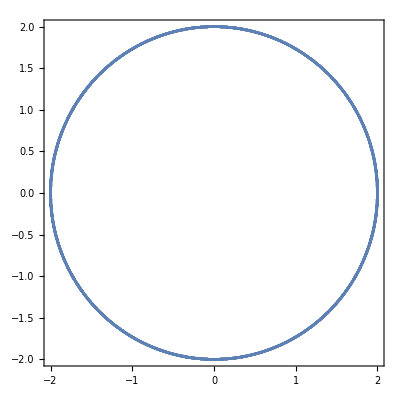

```mathematica
JuliaSetPlot[-z^2/2,z,ColorFunction->None]
```